```mathematica
Inductor = 5;
Resistencia = 10;
Capacitor=0.1;
V=10;
valorn=Sqrt[1/(Capacitor Inductor)-Resistencia^2/(4 Inductor^2)];
(*Caso I -> R^2 < (4L)/C*)
```

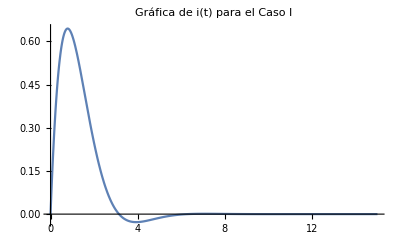

```mathematica
Corriente[t_]=V/(Inductor valorn)*Exp[-(Resistencia t)/(2 Inductor)]*Sin[valorn t];
Plot[Corriente[t],{t,0,15},PlotLabel->Style["Gráfica de i(t) para el Caso I", FontSize->16, Black], PlotRange->All]
```

```mathematica
(*Caso II -> R^2 = (4L)/C *)
```

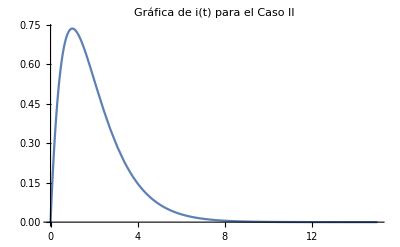

```mathematica
Corriente2[t_]=(V t)/Inductor Exp[-(Resistencia t)/(2 Inductor)];
Plot[Corriente2[t],{t,0,15},PlotLabel->Style["Gráfica de i(t) para el Caso II", FontSize->16, Black], PlotRange->All]
```

```mathematica
(*Caso III ->R^2 > (4 L)/C*)
```

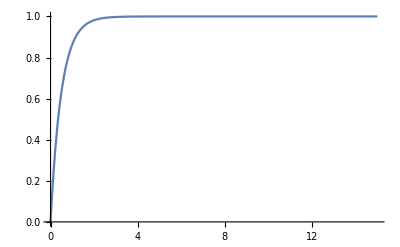

```mathematica
Corriente3[t_]=V/(Inductor (-valorn))Exp[-(Resistencia t)/(2Inductor)]Sinh[(-valorn)t];
Plot[Corriente3[t],{t,0,15},PlotRange->All]
```